# Natural Inflation

# This notebook is a part of my Diploma Thesis with title “Swampland Conjectures and Constraints on Inflation” . The knowledge of the theoretical results is important, if someone wishes to follow the presented results in this notebook. My Thesis can be found in an other file in my GitHub repository.

## Definition of the Potential and Introduction of the Slow-Roll parameters

## In this section we will introduce the potential and the slow-roll parameters

```mathematica
v[x_]:=Λ^4*(1+Cos[l*k*x])
ε1=a/(2*k^2)*(v'[x]/v[x])^2// Simplify;
ε2=-a/k^2*(v''[x]/v[x])+ε1// Simplify;
ε=ε1/a// Simplify;
η=1/k^2*(v''[x]/v[x])// Simplify;
η1=a*η// Simplify;
```

It is required by the theory that the period of inflation should stop when the flatness conditions are a not satisfied, so when ε1 = 1.

```mathematica
Solve[ε1==1,x]
```

{{x→ConditionalExpression[(2 (-ArcTan[(√2)/(√a l)]+π C[1]))/(k l), C[1]∈ℤ]},{x→ConditionalExpression[(2 (ArcTan[(√2)/(√a l)]+π C[1]))/(k l), C[1]∈ℤ]}}

We have to choose second possible solution, so we set with xf the final value for the φ.

```mathematica
xf=(2 (ArcTan[(√2)/(√a l)]))/(k l)// Simplify
```

(2 ArcTan[(√2)/(√a l)])/(k l)

We proceed to the calculation of the initial value of φ , which denoted as xi
Firstly, the integral for the e-folding number is calculated.

```mathematica
Integrate[-(k^2/a)*(v[x]/v'[x]),x]
```

(2 (Log[Cos[(k l x)/2]]+Log[Tan[(k l x)/2]]))/(a l^2)

```mathematica
Solve[(2 Log[Sin[(k l xf)/2]])/(a l^2)-(2 Log[Sin[(k l x)/2]])/(a l^2)==Y,x]
```

{{x→ConditionalExpression[(2 (π-ArcSin[ⅇ^(1/2 (-a l^2 Y+2 Log[(√2)/(√a √(1+2/(a l^2)) l)]))]+2 π C[1]))/(k l), ]},{x→ConditionalExpression[(2 (ArcSin[ⅇ^(1/2 (-a l^2 Y+2 Log[(√2)/(√a √(1+2/(a l^2)) l)]))]+2 π C[1]))/(k l), ]}}

```mathematica
xi=(2 (ArcSin[ⅇ^(1/2 (-a l^2 Y+2 Log[(√2)/(√a √(1+2/(a l^2)) l)]))]))/(k l)// Simplify
```

(2 ArcSin[(√2 ⅇ^(-1/2 a l^2 Y))/(√a √(1+2/(a l^2)) l)])/(k l)

# Calculation of the observational indices

We calculate the slow-roll parameters for
φ = φi and we take the Taylor approximation for N → ∞. Afterwards, we
calculate the primordial density perturbation and the tensor to scalar ratio for φ = φi and we start our primary work.

```mathematica
εi=ε/. x->xi// Simplify;
ε1i=ε1/. x->xi// Simplify;
ε2i=ε2/. x->xi// Simplify;
ηi=η/. x->xi// Simplify;
η1i=η1/. x->xi// Simplify;
```

We set Y=60

```mathematica
εi60=εi/. Y->60// Simplify
ε1i60=ε1i/. Y->60// Simplify
ε2i60=ε2i/.Y->60// Simplify
ηi60=ηi/. Y->60// Simplify
η1i60=η1i/.Y->60// Simplify
```

l^2/(-2+ⅇ^(60 a l^2) (2+a l^2))

(a l^2)/(-2+ⅇ^(60 a l^2) (2+a l^2))

(a l^2)/2

-(l^2 (-4+ⅇ^(60 a l^2) (2+a l^2)))/(-4+2 ⅇ^(60 a l^2) (2+a l^2))

-(a l^2 (-4+ⅇ^(60 a l^2) (2+a l^2)))/(-4+2 ⅇ^(60 a l^2) (2+a l^2))

We proceed with the primordial density perturbation and the tensor to scalar ratio :

```mathematica
ns=1-6*ε1i+2*η1i//Simplify;
r=16*ε1i//Simplify;
r60=r/.Y->60// Simplify
ns60=ns/. Y->60// Simplify
```

(16 a l^2)/(-2+ⅇ^(60 a l^2) (2+a l^2))

-(2+2 a l^2+ⅇ^(60 a l^2) (-2+a l^2+a^2 l^4))/(-2+ⅇ^(60 a l^2) (2+a l^2))

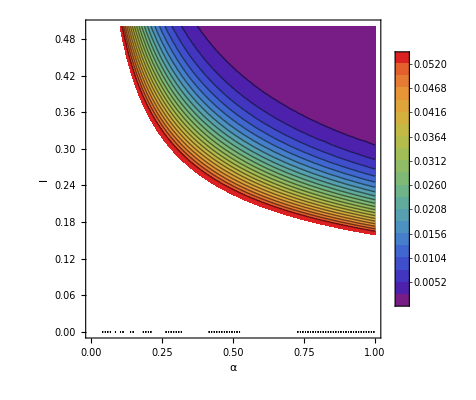

```mathematica
ContourPlot[r60,{a,0,1},{l,0,0.50112},FrameLabel->{"α","l"},PlotLegends->Automatic,ColorFunction->"Rainbow",Contours->20,PlotRange->{0,0.056}]
```

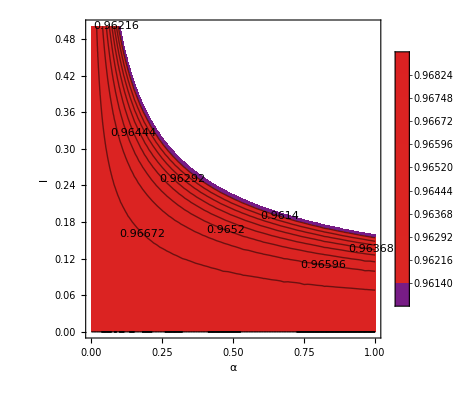

```mathematica
ContourPlot[ns60,{a,0,1},{l,0,0.50112},FrameLabel->{"α","l"},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",Contours->10,PlotRange->{0.9607,0.9691}]
```

We set al^2=q to obtain the following results:

```mathematica
εq=l^2/(-2+ⅇ^(60 q) (2+q))//Simplify;
ε1q=q/(-2+ⅇ^(60 q) (2+q))// Simplify;
ε2q=q/2// Simplify;
ηq=-(l^2 (-4+ⅇ^(60 q) (2+q)))/(-4+2 ⅇ^(60q) (2+q))//Simplify;
η1q=-(q (-4+ⅇ^(60 q) (2+q)))/(-4+2 ⅇ^(60 q) (2+q))// Simplify;
```

```mathematica
Plot[{y=0.02526/x^2,y=1,y=0.02535/x^2},{x,0.0032,0.50112},Frame->True,FrameLabel->{"l","a"},PlotLabels->{0.02526/l^2,a_maximum,0.02535/l^2},PlotRange->{{0.157,0.16},{0.99,1.01}}]
Plot[{y=0.02526/x^2,y=1,y=0.02535/x^2},{x,0.0032,0.50112},Frame->True,FrameLabel->{"l","a"},PlotLabels->{0.02526/l^2,a_maximum,0.02535/l^2},PlotRange->Automatic]
```

-Graphics-

-Graphics-

```mathematica
Plot[{0.02526/l^2,0.02535/l^2},{l,0.0032,0.50112},Frame->True,FrameLabel->{"l","a"},PlotLabels->Automatic,PlotRange->{{0.50111,0.50112},{0.1,0.102}}]
```

-Graphics-

```mathematica
Plot[{ε1q,ε2q,η1q},{q,0.02526,0.02535},Frame->True,FrameLabel->{"αl","Slow-roll parameters arithmetic values"},PlotLabels->{"ε1","ε2","η1"}]
```

-Graphics-

The remaining slow-roll parameters contour plots.

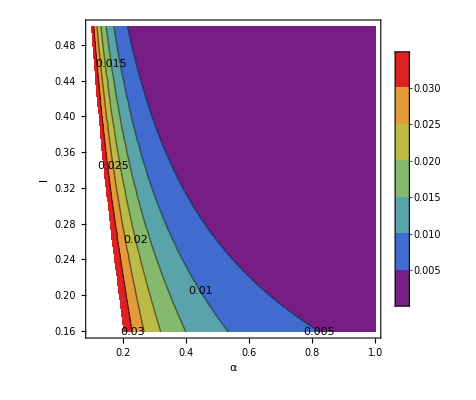

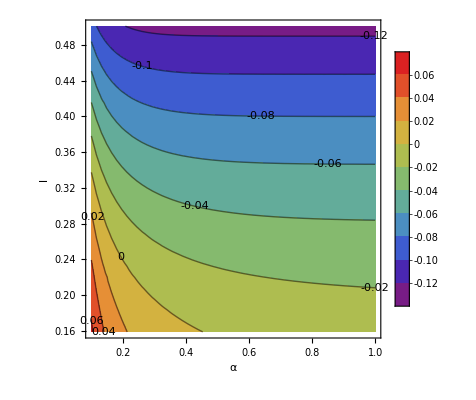

```mathematica
ContourPlot[εi60,{a,0.100589,1},{l,0.158934,0.50112},FrameLabel->{"α","l"},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",Contours->Automatic]
ContourPlot[ηi60,{a,0.100589,1},{l,0.158934,0.50112},FrameLabel->{"α","l"},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",Contours->Automatic]
```

## Swampland Conjectures

• The Swampland Distance Conjecture limits the validity of an E.F.T.
and set an upper limit for the traversable by the scalar field as following

                                  ∆φ ≤ f ∼ O(1), in natural units

• The De Sitter Conjecture. It declares that it is impossible to create
De Sitter vacua in string theory. This leads us to set of a lower limit
for the gradient of scalar potentials [Tri20]:
V’/V≥ g ∼ O(1). 
• Another important result is the following -V”/V≥ g ∼ O(1).

(l^2 (-4+ⅇ^(60 a l^2) (2+a l^2)))/(-4+2 ⅇ^(60 a l^2) (2+a l^2))

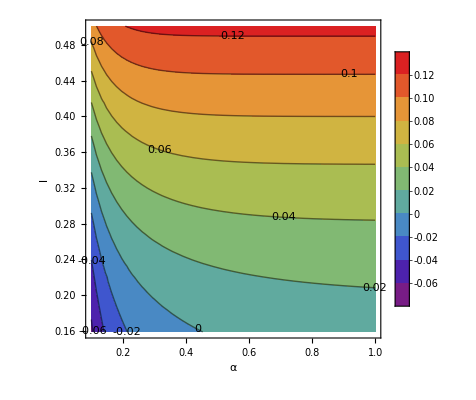

```mathematica
s1=-(v''[x]/v[x]);
s1intial=s1/. x->xi;
s1intial60=s1intial/. Y->60;
s1intial60k=s1intial60/. k->1// Simplify
ContourPlot[s1intial60k,{a,0.100589,1},{l,0.158934,0.50112},FrameLabel->{"α","l"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

-(l (2+a l^2) Sin[2 ArcSin[(√2 ⅇ^(-30 a l^2))/(√a √(1+2/(a l^2)) l)]])/(4-4 ⅇ^(-60 a l^2)+2 a l^2)

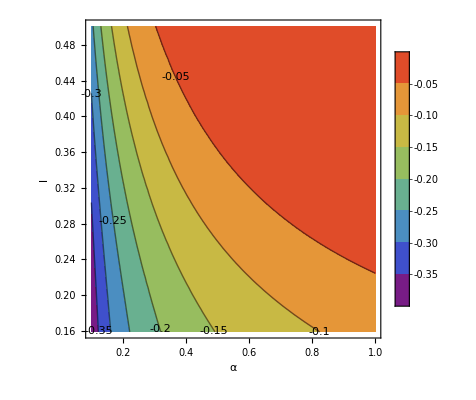

```mathematica
s2=(v'[x]/v[x]);
s2intial=s2/. x->xi;
s2intial=s2/. x->xi;
s2intial60=s2intial/. Y->60;
s2intial60k=s2intial60/. k->1// Simplify
ContourPlot[s2intial60k,{a,0.100589,1},{l,0.158934,0.50112},FrameLabel->{"α","l"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

At this point, we will check the first criterion

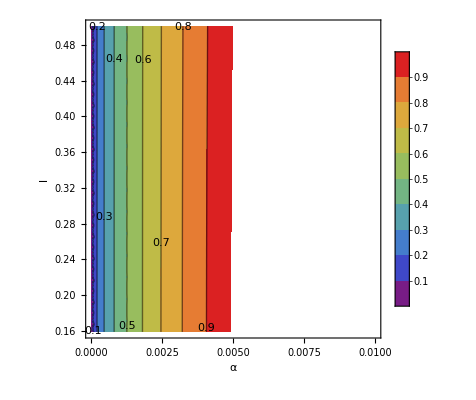

```mathematica
derx=xf-xi;
derx60=derx/.Y->60;
derx60k=derx60/.k->1;
ContourPlot[derx60k,{a,0,0.01},{l,0.1589,0.50112},FrameLabel->{"α","l"},ContourLabels->All,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->{0,0.99}]
```

At this point we have some calculations for a=1. This is the General Relativity limit.

```mathematica
nsgr=ns60/.a->1
```

-(2+2 l^2+ⅇ^(60 l^2) (-2+l^2+l^4))/(-2+ⅇ^(60 l^2) (2+l^2))

```mathematica
Reduce[nsgr>0.9607,l]
Reduce[nsgr<0.9691,l]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.159227<l<0||0<l<0.159227

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

l∈ℝ&&l≠0